## Definition

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.01;u0=10^-20;δstart=10^-10;m=100;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_]:=
Module[{min=1.*10^-19,max=5000,wpc=MachinePrecision,acg=30,sol,ef,evShifted,evnew,steps=∞,stepfraction=10^-2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,WorkingPrecision->wpc,AccuracyGoal->acg];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.97 SetPrecision[evShifted[[n]],3],1.03 SetPrecision[evShifted[[n]],3]},WorkingPrecision->wpc,AccuracyGoal->acg,StepMonitor:>PrintTemporary[e]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_]:=
Module[{efunction,amplitude},efunction=Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]],2];
amplitude=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
amplitude f[rr]/.efunction
]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]]
δexpminus5=δ50e[10^-5,V[r]]
δ50V=δ50[V[r]]
```

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678812640161460360327585430028974190240877271907) 小于 WorkingPrecision (50.).

-0.00067881253589889958676131199718849591989776729252557

NDSolve::precw: 参数函数的精度 ({{200 (1/100000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.213592724017438889916554830764862711831186675021) 小于 WorkingPrecision (50.).

-0.21043067293094009709783969312898709145059320931152

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.778437) is less than WorkingPrecision (50.).

{0.003,-0.6614536026738196707110472379850780307982936756069}    0.703132

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.213592724017438889916554830764862711831186675021) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.21043067293094009709783969312898709145059320931152}    0.7499956

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.28426) is less than WorkingPrecision (50.).

{0.01,-0.909203134411430515651501103567148676726952592023}    1.015635

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.06888) is less than WorkingPrecision (50.).

{0.001,0.81867970935026648367605247945349892294113542543198}    0.671881

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.478119) is less than WorkingPrecision (50.).

{0.007,0.44598979120485669642046632636536898548975762966286}    0.8593841

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.17589) is less than WorkingPrecision (50.).

{0.07,0.17410884318918659480700836719617977293264681050285}    2.796903

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.23368) is less than WorkingPrecision (50.).

{0.03,0.22956086972310478983657790443998025217450623442452}    1.937519

NDSolve::precw: The precision of the differential equation ({{200 (1+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.630566) is less than WorkingPrecision (50.).

{0.1,-0.56259207118956921040892077933931577387608624446855}    3.67191

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.25817) is less than WorkingPrecision (50.).

{0.3,-1.4123448516398016119219178154888250790089753224324}    5.546929

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.506587) is less than WorkingPrecision (50.).

{0.7,-0.46890334708088320279820066308781569831190573235852}    8.2813283

FindRoot::precw: The precision of the argument function (Tan[δ]==-12.76630941561937022736506022645637582875035787) is less than WorkingPrecision (50.).

{1,-1.492624773324020573225483910175221066044107730265}    9.5782171

{-0.21043067293094009709783969312898709145059320931152,0.81867970935026648367605247945349892294113542543198,-0.6614536026738196707110472379850780307982936756069,0.44598979120485669642046632636536898548975762966286,-0.909203134411430515651501103567148676726952592023,0.22956086972310478983657790443998025217450623442452,0.17410884318918659480700836719617977293264681050285,-0.56259207118956921040892077933931577387608624446855,-1.4123448516398016119219178154888250790089753224324,-0.46890334708088320279820066308781569831190573235852,-1.492624773324020573225483910175221066044107730265}

## Determine the best 𝒶 value (using V_eff^(a^2))

```mathematica
aa={10,5,1,0.1,0.05,0.01,0.005};
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[a_,c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_,{c1start_,c1end_}]:=Module[{aaa,findroot},aaa=a;
Print[aaa];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δexpminus10,{c1,c1start,c1end},MaxIterations->200,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
Determinec1[aa[[8]],{-1,0}]
```

Part::partw: {10,5,1,0.1,0.05,0.01,0.005} 的部分 8 不存在.

{10,5,1,0.1,0.05,0.01,0.005}⟦8⟧

Part::partw: {10,5,1,0.1,0.05,0.01,0.005} 的部分 8 不存在.

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+0.01 Power[«2»] Erf[«1»]+0.063493635934240969785763304934636020155053899282273 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

Part::partw: {10,5,1,0.1000000000000000055511151231257827021181583404541,0.050000000000000002775557561562891351059079170227051,0.010000000000000000208166817117216851329430937767029,0.0050000000000000001040834085586084256647154688835144} 的部分 8 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

NDSolve::ndnum: 在 r == 1.×10^-20 处碰到一个导数的非数值量.

ReplaceAll::reps: {NDSolve[{200 (1/10000000000+Times[«3»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

NDSolve::precw: 参数函数的精度 ({{200. (1.×10^-10+0.01 Power[«2»] Erf[«1»]+0.0634936 Power[«2»] Power[«2»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::ndnum: 在 r == 9.9999999999999994515327145420957165172950370278739×10^-21 处碰到一个导数的非数值量.

ReplaceAll::reps: {NDSolve[{200. (1.×10^-10+Times[«3»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-20,(«1»)^(«1»)[«1»]==1.}}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

FindRoot::nlnum: 在 {δ} = {0.} 处，函数值 {0.==(-1.66667×10^-7-1. (-1.+Times[«3»]))/(1414.21+1414.21 Plus[«2»])/.NDSolve[{200. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} 不是由数字组成的维度为 {1} 的列表.

NDSolve::precw: 参数函数的精度 ({{200. (1.×10^-10+0.01 Power[«2»] Erf[«1»]+0.0634936 Power[«2»] Power[«2»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

NDSolve::ndnum: 在 r == 9.9999999999999994515327145420957165172950370278739×10^-21 处碰到一个导数的非数值量.

General::stop: 在本次计算中，NDSolve::ndnum 的进一步输出将被抑制.

FindRoot::nlnum: 在 {δ} = {0.} 处，函数值 {0.==(-1.66667×10^-7-1. (-1.+Times[«3»]))/(1414.21+1414.21 Plus[«2»])/.NDSolve[{200. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，FindRoot::nlnum 的进一步输出将被抑制.

c1/.FindRoot[hhhc1[1/10^10,aaa$71303,c1]==δexpminus10,{c1,-1,0},MaxIterations→200,PrecisionGoal→20,WorkingPrecision→50,StepMonitor:>Print[{c1,evnhhhc1[aaa$71303,c1]}]]

c1/.FindRoot[hhhc1[1/10^10,aaa$71303,c1]==δexpminus10,{c1,-1,0},MaxIterations→200,PrecisionGoal→20,WorkingPrecision→50,StepMonitor:>Print[{c1,evnhhhc1[aaa$71303,c1]}]]

```mathematica
AppendTo[c1a,%]
```

{-3.8645787152119821796374227577035758784997797377196,0.0067108328400632785125076886680881180573983023098904,-1.1553255439184859099440318831455233031961398754704,-0.069202747395969572501186385988258564803748518600798,-0.065898375845764044222985234000589116476476192474364,-0.063427067503092605937897729972974047996103763580321,-0.063128358064980759356554784744730568490922451019286}

```mathematica
c1a=Determinec1[#,{0,-3}]&/@Drop[aa,-1];
```

10

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+0.0190481 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0007925068551956752773073181957) 小于 WorkingPrecision (30.).

NDSolve::precw: 参数函数的精度 ({{200 (1.×10^-10+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0008485748083063111841667678946) 小于 WorkingPrecision (30.).

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+0.0190480907802722909357289914804 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0007925068551956753451715169073) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{-3.25755227512315001146226096588,0.000010226353}

{-3.23629816225417705895177048667,8.3129948×10^-7}

{-3.23441754142275189294839825667,3.9353052×10^-8}

{-3.23432409044260314365804529597,1.4278828×10^-10}

{-3.23432375013108301608547056674,2.4377697×10^-14}

{-3.23432375007297300962862529075,1.5096625×10^-20}

{-3.23432375007297297364222778353,1.6×10^-30}

-3.23432375007297297364222778353

5

{0.,8.6182854×10^-6}

{-3.,-0.000062368223}

{-2.48818,0.00002380608}

{-3.,-0.000062368223}

{-2.89649,-0.00010755385}

{-2.62957,0.00016083339}

{-2.66863,0.0003276012}

{-2.76303,-0.00038869336}

{-2.76285,-0.00039010491}

{-2.73934,-0.00075987212}

{-2.72759,-0.0015042429}

{-2.72171,-0.0030241419}

{-2.71877,-0.0062009636}

{-2.7173,-0.013167263}

{-2.71657,-0.030181819}

{-2.7162,-0.085459986}

{-2.71583,0.10165186}

{-2.71585,0.11555753}

{-2.71594,0.25489189}

{-2.71598,0.60382203}

{-2.71602,-0.8173709}

{-2.71601,-1.1220224}

{-2.716,1.3203307}

{-2.71600271756427602554140321445,-1.458415}

{-2.71599940790289906544785480946,1.4903202}

{-2.71600022687084206593263466749,1.5380408}

{-2.71600108063878530561183247907,-1.5536476}

{-2.71600065375481368577223357328,1.5629881}

{-2.71600086783647989714600127848,-1.566088}

{-2.71600081431690386459112153299,-1.5692171}

{-2.71600081431690386459112153299,-1.5692171}

{-2.71600080091687127885355400352,-1.5700005}

{-2.71600080091687127885355400352,-1.5700005}

{-2.71600080091687127885355400352,-1.5700005}

{-2.71600079924155402309395344707,-1.5700985}

{-2.71600079924155402309395344707,-1.5700985}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 30. 位工作精度以满足这些容差.

{-2.71600079882253210287760209239,0.00067911771}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 30. 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

{-2.71600079882271326487436700225,0.00067911771}

{-2.71600079903213364398416022466,0.00067850736}

{-2.71600079903213364398416022466,0.00067850736}

{-2.71600079903217887405665206344,0.00067850736}

{-2.71600079903217887405665206344,0.00067850736}

{-2.71600079903220147928019083037,0.00067850736}

{-2.71600079905835641653902264001,0.00067850736}

{-2.71600079907143388516843854483,0.00067850736}

{-2.71600079907143388516843854483,0.00067850736}

{-2.71600079907143670960014140319,0.00067850736}

{-2.71600079907143670960014140319,0.00067850736}

{-2.71600079907143812120580899993,0.00067850736}

{-2.71600079907143812120580899993,0.00067850736}

{-2.71600079907143882670372566844,0.00067850736}

{-2.71600079907225510978872607176,0.00067850736}

{-2.71600079907266325133122627341,0.00067850736}

{-2.71600079907266325133122627341,0.00067850736}

{-2.71600079907266333948037237344,0.00067850736}

{-2.71600079907266333948037237344,0.00067850736}

{-2.71600079907266338353590707668,0.00067850736}

{-2.71600079907266338353590707668,0.00067850736}

{-2.71600079907266340555415940864,0.00067850736}

{-2.71600079907266340555415940864,0.00067850736}

{-2.71600079907266341655853013028,0.00067850736}

{-2.71600079907267614895872134862,0.00067850736}

{-2.71600079907268251515881695778,0.00067850736}

{-2.71600079907268251515881695778,0.00067850736}

{-2.71600079907268251653376912535,0.00067850736}

{-2.71600079907268410739631694386,0.00067850736}

{-2.71600079907268410739631694386,0.00067850736}

{-2.71600079907268410773990650679,0.00067850736}

{-2.71600079907268410773990650679,0.00067850736}

{-2.71600079907268410791162708084,0.00067850736}

{-2.71600079907268410791162708084,0.00067850736}

{-2.71600079907268410799745028019,0.00067850736}

{-2.71600079907268420729756908029,0.00067850736}

{-2.71600079907268420729756908029,0.00067850736}

{-2.71600079907268420731901561222,0.00067850736}

{-2.71600079907268420731901561222,0.00067850736}

{-2.71600079907268420732973424622,0.00067850736}

{-2.71600079907268420732973424622,0.00067850736}

{-2.71600079907268420733509124825,0.00067850736}

{-2.71600079907268420733509124825,0.00067850736}

{-2.71600079907268420733776859227,0.00067850736}

{-2.71600079907268420733776859227,0.00067850736}

{-2.71600079907268420733910668604,0.00067850736}

{-2.7160007990726842088873229154,0.00067850736}

{-2.71600079907268420966143103008,0.00067850736}

{-2.71600079907268421004848508742,0.00067850736}

{-2.71600079907268421024201211609,0.00067850736}

{-2.71600079907268421033877563043,0.00067850736}

{-2.71600079907268421033877563043,0.00067850736}

{-2.71600079907268421033879652911,0.00067850736}

{-2.71600079907268421036297695835,0.00067850736}

{-2.71600079907268421037506717297,0.00067850736}

{-2.71600079907268421037506717297,0.00067850736}

{-2.71600079907268421037506978418,0.00067850736}

{-2.71600079907268421037506978418,0.00067850736}

{-2.71600079907268421037507108922,0.00067850736}

{-2.71600079907268421037658106073,0.00067850736}

{-2.71600079907268421037733604648,0.00067850736}

{-2.71600079907268421037771353936,0.00067850736}

{-2.71600079907268421037771353936,0.00067850736}

{-2.71600079907268421037771362088,0.00067850736}

{-2.71600079907268421037771362088,0.00067850736}

{-2.71600079907268421037771366163,0.00067850736}

{-2.71600079907268421037776080749,0.00067850736}

{-2.71600079907268421037778438041,0.00067850736}

{-2.71600079907268421037779616688,0.00067850736}

{-2.71600079907268421037779616688,0.00067850736}

{-2.71600079907268421037779616942,0.00067850736}

{-2.71600079907268421037779616942,0.00067850736}

{-2.71600079907268421037779617069,0.00067850736}

{-2.71600079907268421037779764273,0.00067850736}

{-2.71600079907268421037779764273,0.00067850736}

{-2.71600079907268421037779764305,0.00067850736}

{-2.71600079907268421037779764305,0.00067850736}

{-2.71600079907268421037779764321,0.00067850736}

{-2.71600079907268421037779782705,0.00067850736}

{-2.71600079907268421037779782705,0.00067850736}

{-2.71600079907268421037779782709,0.00067850736}

{-2.71600079907268421037779782709,0.00067850736}

{-2.71600079907268421037779782711,0.00067850736}

{-2.71600079907268421037779785007,0.00067850736}

{-2.71600079907268421037779785007,0.00067850736}

{-2.71600079907268421037779785008,0.00067850736}

{-2.71600079907268421037779785581,0.00067850736}

{-2.71600079907268421037779785868,0.00067850736}

{-2.71600079907268421037779786012,0.00067850736}

{-2.71600079907268421037779786012,0.00067850736}

{-2.71600079907268421037779786013,0.00067850736}

{-2.71600079907268421037779786048,0.00067850736}

{-2.71600079907268421037779786066,0.00067850736}

{-2.71600079907268421037779786066,0.00067850736}

{-2.71600079907268421037779786067,0.00067850736}

{-2.71600079907268421037779786067,0.00067850736}

{-2.71600079907268421037779786068,0.00067850736}

FindRoot::brdig: 根已经被 30. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-20.

-2.71600079907268421037779786069

1

{0.,-0.000073626374}

{0.,-0.000073626374}

{-1.44092,0.0001036302}

{-1.10978,-7.7251206×10^-6}

{-1.13275,-3.9118594×10^-6}

{-1.15546,2.4181007×10^-8}

{-1.15532,-5.8937397×10^-10}

{-1.15533,-9.103986×10^-14}

{-1.15533,-6.8937289×10^-21}

{0,-0.000073626374}

{0,-0.000073626374}

{-1.44092382225139977097059511348,0.0001036302}

{-1.10977964914130997939030742062,-7.7251206×10^-6}

{-1.1327523164112854559359663623,-3.9118594×10^-6}

{-1.15546173886285746972242011411,2.4181007×10^-8}

{-1.15532222385581815352099215894,-5.8937397×10^-10}

{-1.15532554340563120504034298624,-9.1039857×10^-14}

{-1.15532554391847518809964541228,-4.5428355×10^-23}

-1.15532554391847518835555155518

0.1

{0.226889548110491250973102887729,-0.00001255964}

{-0.0934129277253655038115689634012,1.42887×10^-6}

{-0.0671990189737441537856620605562,-1.1455142×10^-7}

{-0.0691445929209949174762003715917,-3.3323878×10^-9}

{-0.06920288696239675733561195746,7.9980434×10^-12}

{-0.0692027473862235165671463134373,-5.5734804×10^-16}

{-0.0692027473959492808785023229195,-1.9785897×10^-22}

{-0.0692027473959492843311571777008,-1.9785897×10^-22}

-0.0692027473959492843311571777008

0.05

{0.0573204669957523787966639466411,-1.9529961×10^-6}

{-0.0707344716791050167363541928919,8.2521658×10^-8}

{-0.0657081419521182337290578535904,-3.2363438×10^-9}

{-0.0658978260708325188429871894913,-9.3540728×10^-12}

{-0.0658983759080535051158207717917,1.0631311×10^-15}

{-0.06589837584556921058650232802,3.3758407×10^-20}

{-0.0658983758455672264124196451624,-2.6678148×10^-22}

{-0.065898375845567241969743898822,1.0507851×10^-22}

-0.065898375845567241969743898822

0.01

{0.,-4.9150956×10^-8}

{-0.0442114,-1.4957625×10^-8}

{-0.0634637,2.8576976×10^-11}

{-0.063427,-5.6003457×10^-14}

{-0.0634271,-4.9762908×10^-19}

{-0.0634271,-3.2407517×10^-24}

{-0.0634270674989195482101940189197,-3.2407517×10^-24}

{-0.0634270674989195482101940189197,-3.2407517×10^-24}

{-0.0634270674989195523653538590814,-3.2407517×10^-24}

{-0.0634270674989195523653538590814,-3.2407517×10^-24}

-0.0634270674989195523653538590814

```mathematica
Module[{aaa,findroot,Solveδ,hhhc1δ,evnhhhc1δ},aaa=aa[[7]];
Solveδ[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];
Print["Start"];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
(*Print[sol];*)
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->20,PrecisionGoal->15];
Print[δs];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
];
hhhc1δ[en_,a_,c1_?NumberQ]:=Solveδ[en,Vs1[r,a,c1]];
evnhhhc1δ[a_,c1_]:=N[hhhc1δ[10^-10,a,c1]-δexpminus10,8];
Print[aaa];findroot=FindRoot[hhhc1δ[10^-10,aaa,c1]==δexpminus10,{c1,-30,-100},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30,StepMonitor:>Print[{c1,evnhhhc1δ[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

0.005

Start

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+380.962 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0006892931100241553960986484023) 小于 WorkingPrecision (30.).

{δ→-0.000689293000857392163581623525416}

Start

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+1269.87 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0006804921121318845059725633368) 小于 WorkingPrecision (30.).

{δ→-0.000680492007093529655273076467495}

Start

NDSolve::precw: 参数函数的精度 ({{200 (1/10000000000+1269.87 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.0006804921121318845059725633368) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{δ→-0.000680492007093529655273076467495}

Start

{δ→-0.000689293000857392163581623525416}

Start

{δ→-0.000680492007093529633513551149347}

Start

{δ→-0.000678342487747159786923488455062}

Start

{δ→-0.000678342487747159786923488455062}

{-113.357921477773920676007953434,4.7004815×10^-7}

Start

{δ→-0.000678342487747159808403524554573}

Start

{δ→-0.000678973196710614662704210183667}

Start

{δ→-0.000678973196710614662704210183667}

{-110.436865515971741709806268128,-1.6066081×10^-7}

Start

{δ→-0.000678973196710614655738883727435}

Start

{δ→-0.000678824747441710406134205133755}

Start

{δ→-0.000678824747441710406134205133755}

{-111.180947571370861986428498648,-1.2211543×10^-8}

Start

{δ→-0.000678824747441710406134205133755}

Start

{δ→-0.000678812194371543538766380845886}

Start

{δ→-0.000678812194371543538766380845886}

{-111.242156292308262971790947661,3.4152736×10^-10}

Start

{δ→-0.000678812194371543538766380845886}

Start

{δ→-0.000678812536607085464480966769133}

Start

{δ→-0.000678812536607085464480966769133}

{-111.240491006255054942841760079,-7.0818514×10^-13}

Start

{δ→-0.000678812536607085464480966769133}

Start

{δ→-0.000678812535898941144659443488353}

Start

{δ→-0.000678812535898941144659443488353}

{-111.240494452217547384012504379,-4.0822776×10^-17}

Start

{δ→-0.000678812535898941144659443488353}

Start

{δ→-0.000678812535898900485730783162415}

Start

{δ→-0.000678812535898900485730783162415}

{-111.240494452416198633414353852,-1.6384704×10^-19}

Start

{δ→-0.000678812535898900485730783162415}

Start

{δ→-0.000678812535898900323919530288515}

Start

{δ→-0.000678812535898900323919530288515}

{-111.240494452416999156685088956,-2.0357838×10^-21}

Start

{δ→-0.000678812535898900323919530288515}

Start

{δ→-0.000678812535898900323919530288515}

Start

{δ→-0.000678812535898900323919530288515}

{-111.240494452417009228248816348,-2.0357838×10^-21}

-111.240494452417009228248816348

-111.240494452417009228248816348

```mathematica
c1a[[7]]=%
```

-208.089556194043885391093314738

```mathematica
AppendTo[c1a,%]
```

{-3.23432375007297297364222778353,-208.089556194043885391093314738,-1.15532554391847518835555155518,-0.0692027473959492843311571777008,-0.065898375845567241969743898822,-0.0634270674989195523653538590814,-111.240494452417009228248816348}

```mathematica
c1a
```

{-3.8645787152119821796374227577035758784997797377196,0.0067108328400632785125076886680881180573983023098904,-1.1553255439184859099440318831455233031961398754704,-0.069202747395969572501186385988258564803748518600798,-0.065898375845764044222985234000589116476476192474364,-0.063427067503092605937897729972974047996103763580321,-0.063128358064980759356554784744730568490922451019286}

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)-1}];
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934231356693915641592) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812032286090557722723178}    1.765642

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.242395) is less than WorkingPrecision (30.).

{0.003,-0.237808025258942968454592217633}    2.375024

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229787554680574091352715686) is less than WorkingPrecision (30.).

{1/100000,-0.225866607030782472690896833346}    1.937518

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.279767) is less than WorkingPrecision (30.).

{0.03,0.272792426851204486218475909799}    4.531294

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.441078) is less than WorkingPrecision (30.).

{0.007,0.415409783809699716181516250067}    2.875026

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.744153) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,0.639748753189830391142836075742}    2.57815

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.921205) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.74440779155935832037209268735}    3.046904

FindRoot::precw: The precision of the argument function (Tan[δ]==1.88299) is less than WorkingPrecision (30.).

{0.07,1.08260231015661993929353202968}    6.421935

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.38527) is less than WorkingPrecision (30.).

{0.3,-0.945535217058042382806255556143}    13.953262

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.473837) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.442498874307010800292363004889}    7.5000716

FindRoot::precw: The precision of the argument function (Tan[δ]==0.557637) is less than WorkingPrecision (30.).

{0.7,0.508687312251855852292990713136}    17.422034

NDSolve::precw: The precision of the differential equation ({{200 (1+0.00051675465390043150185502443396194572033242511159995 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==2.9310030062199363746981463) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.24200035336288086567041188579}    18.843929

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934238223795462452829) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812039153188587044745844}    2.203146

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.827065) is less than WorkingPrecision (30.).

{0.003,-0.69102767073302426911321116977}    2.656276

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818877757382274871676839) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.523074) is less than WorkingPrecision (30.).

{1/100000,-0.225896358924420603005870024844}    1.765642

{0.03,-0.481935699918097009650912129687}    4.18754

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0211075) is less than WorkingPrecision (30.).

{0.007,0.0211044055476770780264007939278}    2.937528

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.31462) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.2777864859494378331484289813}    2.984404

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.565047) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.514321945216393408233571065699}    3.015654

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0000403752) is less than WorkingPrecision (30.).

{0.07,-0.0000403751748151259667812618241813}    6.781315

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.86345) is less than WorkingPrecision (30.).

{0.3,-1.07826895307875400614548320775}    13.312626

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.449704) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.422607814961782133540284740827}    6.703188

FindRoot::precw: The precision of the argument function (Tan[δ]==0.895719) is less than WorkingPrecision (30.).

{0.7,0.730444614212567124981860002958}    14.781388

NDSolve::precw: The precision of the differential equation ({{200 (1+0.015180157654949178764279889312006354702461270106502 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==24.756260463371931245304869) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.530424452119108186113099025}    17.078286

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934233693006605399361) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812034622402050766765247}    1.859393

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.834591) is less than WorkingPrecision (30.).

{0.003,-0.695479858228020837210083133775}    2.515649

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.499917) is less than WorkingPrecision (30.).

{0.03,0.463581427398819014741802566224}    3.515658

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229819766538541587988687511) is less than WorkingPrecision (30.).

{1/100000,-0.225897203117880763429980926264}    2.390647

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.330196) is less than WorkingPrecision (30.).

{0.007,-0.31892468112908755742878559028}    2.750027

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==3.0125) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.25029131841785561078183033398}    2.343774

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.728215) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.629412088205582776930685829415}    2.328146

FindRoot::precw: The precision of the argument function (Tan[δ]==0.243098) is less than WorkingPrecision (30.).

{0.07,0.238471903623707057255361210291}    4.796922

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.83666) is less than WorkingPrecision (30.).

{0.3,-1.07221029559694897015093431854}    9.2813369

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.258935) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.25336997725452626418404309318}    5.015671

FindRoot::precw: The precision of the argument function (Tan[δ]==0.618861) is less than WorkingPrecision (30.).

{0.7,0.554172599021471615319733896599}    11.171981

NDSolve::precw: The precision of the differential equation ({{200 (1+0.17841403031981232651128502722977359153837918872548 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==2.0391428253479597867256451) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.11485644691582756236947221062}    12.125413

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934242552718146125003) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812043482109053341983458}    1.546892

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830166) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.003,-0.692865881884370312661629617256}    1.843769

NDSolve::precw: The precision of the differential equation ({{200 (0.007+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.627543) is less than WorkingPrecision (30.).

{0.03,0.560425573584078565224030060109}    3.046904

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.22981898429502719956866788) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{1/100000,-0.22589646011738303408573915309}    1.70314

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.111092) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.001+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.007,-0.110637910941697089397433969284}    2.109398

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{200 (0.01+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.22732) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.270323264131670030314886308}    1.484397

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.674526) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.593423821983585025630975218944}    2.156267

FindRoot::precw: The precision of the argument function (Tan[δ]==0.375494) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.57831) is less than WorkingPrecision (30.).

{0.07,0.359203790326174611559552161403}    4.406291

{0.3,-1.00604418731991915633058614026}    7.6094479

NDSolve::precw: The precision of the differential equation ({{200 (0.1+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.7+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00735536) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,-0.00735522447508504384482548069207}    3.718787

FindRoot::precw: The precision of the argument function (Tan[δ]==0.771392) is less than WorkingPrecision (30.).

{0.7,0.657052002652187785316148879143}    8.6094548

NDSolve::precw: The precision of the differential equation ({{200 (1+1.10562 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==8.9739925112056042266151271) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.4598210332026957296868186807}    9.8282187

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934240801436116502156) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812041730827920766545964}    1.281263

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830112) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.003,-0.692834052948703514776054183474}    1.562516

NDSolve::precw: The precision of the differential equation ({{200 (0.007+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818975167903481596511727) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.630569) is less than WorkingPrecision (30.).

{1/100000,-0.22589645144814064084320692228}    1.343765

{0.03,0.56259416647846395468027127453}    2.640651

NDSolve::precw: The precision of the differential equation ({{200 (0.001+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.109187) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{0.007,-0.108755859592028377256221377867}    1.984393

FindRoot::precw: The precision of the argument function (Tan[δ]==3.23016) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{0.001,1.2705722185316596364276721826}    1.484388

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673738) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592882163637203534945893842968}    2.078145

FindRoot::precw: The precision of the argument function (Tan[δ]==0.380035) is less than WorkingPrecision (30.).

{0.07,0.363177414002682750529784805347}    4.015663

NDSolve::precw: The precision of the differential equation ({{200 (0.1+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.5706) is less than WorkingPrecision (30.).

{0.3,-1.00382856917583202052355973876}    7.9063255

NDSolve::precw: The precision of the differential equation ({{200 (0.7+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.00575547) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.00575541112518823715407133479177}    3.921914

FindRoot::precw: The precision of the argument function (Tan[δ]==0.784482) is less than WorkingPrecision (30.).

{0.7,0.665206844024445528608611520251}    9.031335

NDSolve::precw: The precision of the differential equation ({{200 (1+1.35421 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==9.4466664154945836317915032) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.46533164703942667611019442}    10.093845

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934258736150809178982) is less than WorkingPrecision (30.).

{1/10000000000,-0.000715697812059665533426865153223}    3.343781

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830064) is less than WorkingPrecision (30.).

{0.003,-0.692805621981951147871308501055}    3.812535

NDSolve::precw: The precision of the differential equation ({{200 (0.007+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.229818967055345676221037713) is less than WorkingPrecision (30.).

{1/100000,-0.22589644374256630199932980302}    3.906294

NDSolve::precw: The precision of the differential equation ({{200 (0.001+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.107489) is less than WorkingPrecision (30.).

{0.007,-0.107077757952858492071076420031}    5.234425

FindRoot::precw: The precision of the argument function (Tan[δ]==0.633416) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

{0.03,0.564628119190840330295936738451}    9.843842

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{200 (0.07+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.2327) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.2707942182214262994995456396}    3.671902

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673026) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592392007214012146038788272337}    5.812554

FindRoot::precw: The precision of the argument function (Tan[δ]==0.384592) is less than WorkingPrecision (30.).

{0.07,0.367153621404912310015559094039}    10.578225

NDSolve::precw: The precision of the differential equation ({{200 (0.1+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.56086) is less than WorkingPrecision (30.).

{0.3,-1.00100609165858388936121612581}    24.031475

NDSolve::precw: The precision of the differential equation ({{200 (0.7+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0198492) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.1,0.0198466155605113736558123963219}    11.265732

FindRoot::precw: The precision of the argument function (Tan[δ]==0.810761) is less than WorkingPrecision (30.).

{0.7,0.681267892268641766355873337802}    24.953361

NDSolve::precw: The precision of the differential equation ({{200 (1+4.39393 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==10.521784614051349852524869) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1,1.476040035417158988378899125}    28.390895

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::precw: The precision of the differential equation ({{200 (0.3+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000715697934243931559472633214) is less than WorkingPrecision (30.).

{1/10000000000,-0.00071569781204486094967357558055}    391.6287

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.830064) is less than WorkingPrecision (30.).

{0.003,-0.692805480294573797565498223617}    464.535639

NDSolve::precw: The precision of the differential equation ({{200 (0.007+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.22981896701022439428710404) is less than WorkingPrecision (30.).

{1/100000,-0.225896443699708623673190181564}    430.269692

NDSolve::precw: The precision of the differential equation ({{200 (0.001+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10748) is less than WorkingPrecision (30.).

{0.007,-0.107069411497371239338074786125}    705.694167

NDSolve::precw: The precision of the differential equation ({{200 (0.01+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.63343) is less than WorkingPrecision (30.).

{0.03,0.564638429931464124827139146512}    1179.464263

NDSolve::precw: The precision of the differential equation ({{200 (0.07+40.2721 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (Tan[δ]==3.23272) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.001,1.270795325042822266021876944}    492.879653

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.673022) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{0.01,-0.592389553851644493092361333422}    607.721373

$Aborted

```mathematica
δa=δa~Join~Evaluate[δ50[Vs1[r,aa[[8]],c1a[[8]]]]]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)}];
Δa=Abs[δa[[#]]-δ50V]&/@Range@Length[aa];
La=Transpose@({Drop[ee,1]}~Join~{Δa[[#]]})&/@Range@Length[aa];
```

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.215071658114868401765349286761258188699472045575) is less than WorkingPrecision (50.).

{1/100000,-0.2118446510802907104175579437852583905479976547997}    2.062521

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.792519) is less than WorkingPrecision (50.).

{0.003,-0.67016270580545973913022695320470845319152045282765}    3.593784

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.05167) is less than WorkingPrecision (50.).

{0.001,0.81057798647627759149624722390197580071660658777626}    3.46878

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.882057) is less than WorkingPrecision (50.).

{0.01,-0.72281280153474947554210532326531227927828600965995}    5.578176

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.447396) is less than WorkingPrecision (50.).

{0.007,0.420686244653568484530584206970637093261018631967}    6.000055

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.218832) is less than WorkingPrecision (50.).

{0.07,0.21543601734255679099314374927886282230900666791148}    15.297019

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.250259) is less than WorkingPrecision (50.).

{0.03,0.24522243119432072029475236553000448998741427668795}    10.281347

NDSolve::precw: The precision of the differential equation ({{200 (1+0.024537615398288631085346436827853883866659161344392 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0587397) is less than WorkingPrecision (50.).

{0.1,0.058672328991273180820123553818335616241257642751766}    17.953294

FindRoot::precw: The precision of the argument function (Tan[δ]==-3.37853) is less than WorkingPrecision (50.).

{0.3,-1.283025223035686404626959565569939928506260107132}    32.167468

FindRoot::precw: The precision of the argument function (Tan[δ]==0.684891) is less than WorkingPrecision (50.).

{0.7,0.60051327920613342292146260913145080670080256765113}    44.667584

FindRoot::precw: The precision of the argument function (Tan[δ]==11.22636000109046667985679521750500450313941241) is less than WorkingPrecision (50.).

{1,1.48195473684161162931642314011536898863537476592}    50.288976

NDSolve::precw: The precision of the differential equation ({{200 (1/100000-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.213446815932946593543067140058461040140047788063) is less than WorkingPrecision (50.).

{1/100000,-0.21029112684911236433551119683508897687034606985523}    1.188627

NDSolve::precw: The precision of the differential equation ({{200 (0.001-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.258968) is less than WorkingPrecision (50.).

{0.003,-0.25340081138225242712259456333589088110339199541766}    2.813641

NDSolve::precw: The precision of the differential equation ({{200 (0.007-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.17791) is less than WorkingPrecision (50.).

{0.001,0.866905597628574944914408488174496932451525577009}    1.687515

NDSolve::precw: The precision of the differential equation ({{200 (0.1-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.912753) is less than WorkingPrecision (50.).

{0.01,-0.73981653276698633450086488223735757104037962428285}    6.094921

NDSolve::precw: The precision of the differential equation ({{200 (0.03-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0226564) is less than WorkingPrecision (50.).

{0.007,0.022652510467188192458174763529765069175383393865945}    4.906297

NDSolve::precw: The precision of the differential equation ({{200 (0.3-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.576333) is less than WorkingPrecision (50.).

{0.03,0.52283542631907654140842103880993389248980101923813}    10.718854

NDSolve::precw: The precision of the differential equation ({{200 (0.7-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0665131) is less than WorkingPrecision (50.).

{0.07,0.066415280065920974224074262136665749861809746698969}    22.141948

NDSolve::precw: The precision of the differential equation ({{200 (1-0.000085219035432505232669474329819859237524229279483871 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.1205) is less than WorkingPrecision (50.).

{0.1,-0.11992141998394711457363142178091362870280990325302}    24.500232

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.902579) is less than WorkingPrecision (50.).

{0.3,-0.73423795629498689122600866004397535623714604623384}    40.422256

FindRoot::precw: The precision of the argument function (Tan[δ]==1.0424) is less than WorkingPrecision (50.).

{0.7,0.80615383691652344765139902132099062466015369384379}    53.250503

FindRoot::precw: The precision of the argument function (Tan[δ]==-42.17070009370560252882501622398393317489886739) is less than WorkingPrecision (50.).

{1,-1.54708762328236497255124414549595921340322617074}    55.375538

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.213614741312586072481897148246133239780746171096) is less than WorkingPrecision (50.).

{1/100000,-0.21045172948793881029029731574572657604755030298533}    1.421874

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.820313) is less than WorkingPrecision (50.).

{0.003,-0.68700469492395950454132814827925940293747980298939}    2.109382

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.04146) is less than WorkingPrecision (50.).

{0.001,0.80570519026825589120487726737067667063941608726984}    1.781267

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-5.52441) is less than WorkingPrecision (50.).

{0.01,-1.3917206456992599403290535778410689198368627860853}    4.421902

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.415963) is less than WorkingPrecision (50.).

{0.007,0.39419105960230144506693394030555463338020577471694}    3.093794

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.207483) is less than WorkingPrecision (50.).

{0.07,-0.20458037249127649650551751222762880505513659621454}    10.906338

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.790348) is less than WorkingPrecision (50.).

{0.03,0.66882765159680709595305412899759612973319858875511}    6.625063

NDSolve::precw: The precision of the differential equation ({{200 (1+0.073355819471089270687299982000559054400414050855016 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.362149) is less than WorkingPrecision (50.).

{0.1,-0.34745642918533974658400893331825489898125831556385}    13.609504

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.92335) is less than WorkingPrecision (50.).

{0.3,-1.0913358656115144098924005246728004675759217871625}    21.45333

FindRoot::precw: The precision of the argument function (Tan[δ]==0.389848) is less than WorkingPrecision (50.).

{0.7,0.37172386789965215444788235638269765986974399754838}    29.37529

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.199055463280012765654537146515690276499907634) is less than WorkingPrecision (50.).

{1,-1.337002462568548536444281310975654500219102950752}    32.375319

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.213592738961091704468797725375236331640562642167) is less than WorkingPrecision (50.).

{1/100000,-0.21043068722258171101345009563829377690733949322069}    0.8437735

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.778471) is less than WorkingPrecision (50.).

{0.003,-0.66147504979702456722265597821493054739707588030473}    1.593779

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.06886) is less than WorkingPrecision (50.).

{0.001,0.81867123581245973392365447839727359941324681294763}    1.187509

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.28457) is less than WorkingPrecision (50.).

{0.01,-0.90932268353993295224819023101711883161999732493346}    2.703165

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.478051) is less than WorkingPrecision (50.).

{0.007,0.44593505311509227092614471417354246530824654760847}    2.015647

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.175466) is less than WorkingPrecision (50.).

{0.07,0.17369804000637755655602892914181146284640858012396}    6.390686

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.233396) is less than WorkingPrecision (50.).

{0.03,0.2292909523052549342309742082303405966217825586621}    4.343782

NDSolve::precw: The precision of the differential equation ({{200 (1+0.0439393 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.634143) is less than WorkingPrecision (50.).

{0.1,-0.56514697974467423298111672223102383548659451316108}    7.7656982

FindRoot::precw: The precision of the argument function (Tan[δ]==-7.45523) is less than WorkingPrecision (50.).

{0.3,-1.437458114000662175674857732538628061547498010553}    12.093867

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.85339) is less than WorkingPrecision (50.).

{0.7,-0.70645878067830030007196659325231436815325211578469}    17.578294

FindRoot::precw: The precision of the argument function (Tan[δ]==-13.9999546674338703426861632638243171462437242) is less than WorkingPrecision (50.).

{1,-1.499488631894316071027003475542744839197572130052}    20.04706

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.213592725076520409957661291007082449104422582372) is less than WorkingPrecision (50.).

{1/100000,-0.21043067394381250219938273533553735704251860557526}    1.140636

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.778439) is less than WorkingPrecision (50.).

{0.003,-0.66145512910490821042003704793674773523535899522425}    2.390647

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.06888) is less than WorkingPrecision (50.).

{0.001,0.81867910801959763580620863308274275639045334178967}    1.625016

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.28428) is less than WorkingPrecision (50.).

{0.01,-0.90921171958177413323003298066222758927910674526837}    3.531283

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.478114) is less than WorkingPrecision (50.).

{0.007,0.44598587331166823512431869591298790972467587116542}    2.593775

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.233659) is less than WorkingPrecision (50.).

{0.03,0.22954096894491547583479765524874031619824518531473}    4.453167

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.175857) is less than WorkingPrecision (50.).

{0.07,0.17407684755245907381133083592949934313282168819898}    8.1094505

NDSolve::precw: The precision of the differential equation ({{200 (1+0.0836825 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.630852) is less than WorkingPrecision (50.).

{0.1,-0.56279664403236194559718539781867182473034409246404}    8.4375795

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.35741) is less than WorkingPrecision (50.).

{0.3,-1.414778010536531677698137923114082240439391807352}    13.454727

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.546981) is less than WorkingPrecision (50.).

{0.7,-0.50052256477032730289108571291536647907762406595127}    18.394687

FindRoot::precw: The precision of the argument function (Tan[δ]==-12.98198661882140566644224007958657036865321042) is less than WorkingPrecision (50.).

{1,-1.493918328297706091430313278389176512035159615821}    20.863473

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.213592724019309487803618084493993026975875951714) is less than WorkingPrecision (50.).

{1/100000,-0.21043067293272907834753920470734649815992242357414}    1.218755

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.778437) is less than WorkingPrecision (50.).

{0.003,-0.66145360537339472494711580699531288509881548775588}    3.781279

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.06888) is less than WorkingPrecision (50.).

{0.001,0.81867970828771567932797382016495753019665737958132}    2.84378

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.28426) is less than WorkingPrecision (50.).

{0.01,-0.90920314964018016979366051214697000176295083616383}    6.671932

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.478119) is less than WorkingPrecision (50.).

{0.007,0.44598978426373515656361000416630216632405399940534}    5.687554

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.23368) is less than WorkingPrecision (50.).

{0.03,0.22956083411762137397927387537369909703175052993808}    13.093878

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.17589) is less than WorkingPrecision (50.).

{0.07,0.17410878493989154692943966088441140395980999802541}    21.047067

NDSolve::precw: The precision of the differential equation ({{200 (1+0.402722 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.630567) is less than WorkingPrecision (50.).

{0.1,-0.56259244808434826938526139369152550819718663619645}    24.080653

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.25837) is less than WorkingPrecision (50.).

{0.3,-1.4123497036049789740489967745137232084389997127782}    39.943561

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.506679) is less than WorkingPrecision (50.).

{0.7,-0.46897635687554203445902077030354159488131538443544}    57.586707

FindRoot::precw: The precision of the argument function (Tan[δ]==-12.7668729986272180673508676637622376912746539) is less than WorkingPrecision (50.).

{1,-1.492628210102282298863119251239326039586378395319}    65.354875

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.213592724017557244014186421650988030912855298257) is less than WorkingPrecision (50.).

{1/100000,-0.21043067293105328725108022095536472524287581185962}    7.1875561

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.06888) is less than WorkingPrecision (50.).

{0.001,0.81867970928303728370944210629381857720270559120009}    16.398213

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.778437) is less than WorkingPrecision (50.).

{0.003,-0.66145360284463065145226348631122401355147996672839}    26.038918

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.28426) is less than WorkingPrecision (50.).

{0.01,-0.90920313537509343365680690192424946018106808965773}    48.039124

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.478119) is less than WorkingPrecision (50.).

{0.007,0.44598979076564573163538687228855638250810262284185}    47.879944

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.23368) is less than WorkingPrecision (50.).

{0.03,0.22956086746941581264741093580451622021542156985714}    96.2902745

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.17589) is less than WorkingPrecision (50.).

{0.07,0.17410883950025761469003608483388847775769101003488}    190.666577

NDSolve::precw: The precision of the differential equation ({{200 (1+0.80165 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.630566) is less than WorkingPrecision (50.).

{0.1,-0.56259209506786362813419440451084831871127882570372}    210.769817

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.25819) is less than WorkingPrecision (50.).

{0.3,-1.4123451598575476037294361218341948313419084962545}    322.677078

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.506593) is less than WorkingPrecision (50.).

{0.7,-0.46890800963475438825970454630736763868898434034245}    418.311338

FindRoot::precw: The precision of the argument function (Tan[δ]==-12.76634555182170244399012655645952687746043302) is less than WorkingPrecision (50.).

{1,-1.492624993694778145850052582013356269713382269292}    425.989245

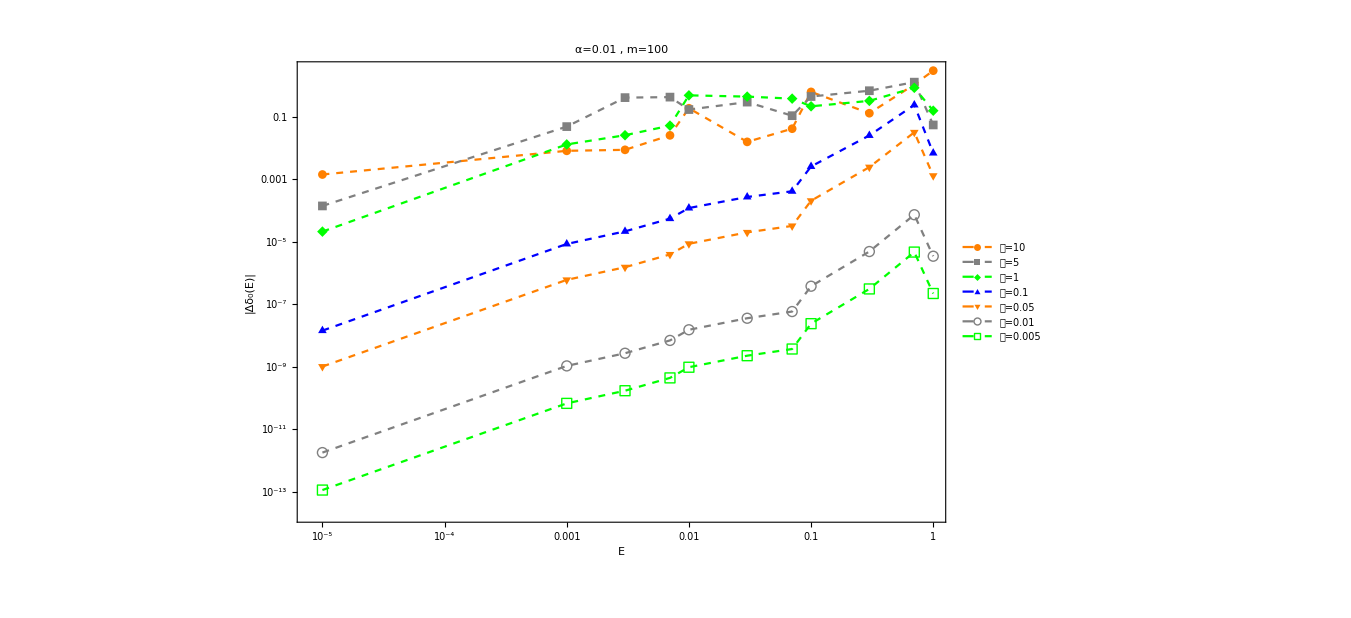

```mathematica
ListLogLogPlot[Table[La[[n]],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->1000,FrameLabel->{"E","|Δδ_0(E)|"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->(("𝒶="<>ToString[#])&/@aa),PlotLabel->Style[("α="<>ToString@α<>" ,  m="<>ToString@m),20]]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_Coulomb_2_Various_a_1.eps",%];
```

```mathematica
a=0.01;
```

## Calculating eigenenergy of Coulomb Potential

```mathematica
EigenEnergy[V[r],αSch]
```

## Determine 𝒸_1 in V_eff^(a^2)

```mathematica
hhhc[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc[c1_]:=N[hhhc[10^-10,c1]-δ50e[10^-10,V[r]],8];
Determinec1:=Module[{aaa,findroot},aaa=a;
Print[a];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δ50e[10^-10,V[r]],{c1,-40},MaxIterations->10000,AccuracyGoal->30,PrecisionGoal->30,WorkingPrecision->80,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1
```

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch]
```

```mathematica
δVs1=δ50[Vs1[r,a,c1]]
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,c2,d1]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δ50e[ee[[1]],V[r]],8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δ50e[ee[[2]],V[r]],8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δ50e[ee[[1]],V[r]],hhh[ee[[2]],c2,d1]==δ50e[ee[[2]],V[r]]},{{c2,-40.},{d1,3.}},MaxIterations->10000,AccuracyGoal->12,WorkingPrecision->50,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch]
```

```mathematica
δVs2=δ50[Vs2[r,a,{c2,d1}]]
```

## Matrix element <p^4>

```mathematica
nRange=20;
```

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[efVs2[[n]],{r}]^2),{r,0,b},opt]+γ/a NIntegrate[efVs2[[n]]^2 δa[r],{r,0,b},opt]+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
REAL=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange}];
REF=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange-2,nRange}];
```

### Matrix element in V_eff^(a^2)

```mathematica
efVs1=Module[{ef,am},
ef=Eigenfun[Vs1[r,a,c1],energyVs1];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs1=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

### Matrix element in V_eff^(a^4)

```mathematica
efVs2=Module[{ef,am},
ef=Eigenfun[Vs2[r,a,c1],energyVs2];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs2=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSE)/REAL);
N[%,6]
```

```mathematica
RESVs2=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs2=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs2;
N[%,6]
Abs[(p4Vs2-REAL)/REAL];
N[%,6]
```